# Code Appendix

## Data Import

### Import

Import metadata such as the position of each of the feeding stations, water station and the corners of the paddock.

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Create a Graphics Boundary of the paddock

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

Import the raw GPS data, so the X and Y coordinates as well as the time stamps and IDS.

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

### Transform to full coordinates

The dataset has 51 sheep(+header) and 210352 time steps

Create two versions of the coordinates, one with missing data as Missing[] for more computational tasks and one with missing data as “Indeterminate” for mathematical tasks

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx",rawCoordinates]*)
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates2.mx",rawCoordinates2]*)
```

I exported the files so the formatting didn’t have to be re-done every time (more efficient) and commented out the export statements so they are not accidentally re-run.

```mathematica
rawCoordinates=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates2.mx"];
```

### Split into 4 intervals

Separate into the four time periods of consecutive data

```mathematica
separatedTs=Rest[Split[rawTs[[All,2]],#2-#1<7&]];
```

```mathematica
splitSequences = Prepend[Accumulate[Length/@separatedTs],0];
```

Again, generating the rawCoordinates and rawCoordinates2 and exporting.

```mathematica
splitRawCoordinates=BlockMap[rawCoordinates[[All,#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitRawCoordinates2=splitRawCoordinates/.Missing[]->Indeterminate;
```

Export

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates.mx",splitRawCoordinates]*)
```

```mathematica
(*Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates2.mx",splitRawCoordinates2]*)
```

Import

```mathematica
splitRawCoordinates=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates.mx"];
```

```mathematica
splitRawCoordinates2=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/splitRawCoordinates2.mx"];
```

This yields four datasets with varying lengths.

```mathematica
Length[#[[1]]]&/@splitRawCoordinates
```

{53417,51685,52387,52862}

### Available Data

```mathematica
availableData=Length[DeleteCases[rawCoordinates[[#]],{Missing[],Missing[]}]]&/@Range[51];
```

```mathematica
splitAvailableData=Table[Length[DeleteCases[splitRawCoordinates[[x,#]],{Missing[],Missing[]}]],{x,1,4}]&/@Range[51];
```

```mathematica
Grid[Prepend[MapIndexed[Prepend[#1,#2[[1]]]&,splitAvailableData],{"Sheep","Rep 1", "Rep 2", "Rep 3", "Rep 4"}],Frame->All]
```

Sheep | Rep 1 | Rep 2 | Rep 3 | Rep 4
1 | 51928 | 51574 | 52249 | 52733
2 | 53353 | 51542 | 52305 | 52803
3 | 53380 | 50355 | 52366 | 52816
4 | 53368 | 51586 | 52339 | 52792
5 | 53342 | 51593 | 52283 | 52751
6 | 52431 | 51631 | 52323 | 50427
7 | 53272 | 51540 | 52262 | 52785
8 | 53332 | 51600 | 52289 | 50614
9 | 53360 | 51644 | 52330 | 52832
10 | 53363 | 51606 | 52297 | 52787
11 | 53378 | 51612 | 52005 | 52800
12 | 53321 | 263 | 52293 | 52761
13 | 42130 | 51567 | 52256 | 52740
14 | 53360 | 51653 | 52368 | 52784
15 | 50742 | 51629 | 52314 | 52783
16 | 53327 | 51548 | 52304 | 52787
17 | 53377 | 51644 | 52340 | 52796
18 | 53293 | 51550 | 52263 | 52756
19 | 52045 | 51585 | 52282 | 52614
20 | 53303 | 51592 | 52284 | 52799
21 | 53282 | 51576 | 52259 | 52739
22 | 53383 | 51655 | 52353 | 52806
23 | 53360 | 0 | 0 | 0
24 | 53343 | 51584 | 52287 | 52801
25 | 53292 | 51416 | 52277 | 52732
26 | 53346 | 51636 | 52358 | 52810
27 | 51922 | 51575 | 50983 | 52767
28 | 53110 | 51476 | 52280 | 52722
29 | 53258 | 51522 | 52245 | 52701
30 | 50835 | 51661 | 52346 | 52806
31 | 53288 | 51597 | 52294 | 52802
32 | 53209 | 51197 | 52326 | 52792
33 | 53373 | 51609 | 52313 | 51069
34 | 53343 | 51621 | 52330 | 52808
35 | 53340 | 51564 | 52285 | 52732
36 | 53356 | 51613 | 52312 | 52778
37 | 53365 | 51600 | 52262 | 52787
38 | 53361 | 51536 | 52372 | 52799
39 | 53351 | 51597 | 51787 | 52774
40 | 53325 | 51604 | 52314 | 52782
41 | 53324 | 51620 | 52320 | 52801
42 | 53330 | 50699 | 52326 | 52789
43 | 51655 | 51625 | 52344 | 52808
44 | 53335 | 51623 | 52341 | 52802
45 | 53255 | 51505 | 52202 | 52653
46 | 53288 | 51632 | 52315 | 52765
47 | 53317 | 51586 | 52322 | 52787
48 | 53286 | 51586 | 52269 | 52812
49 | 52633 | 51547 | 52300 | 52780
50 | 0 | 0 | 52307 | 52800
51 | 53304 | 51551 | 52262 | 52735

### Sheep 23 tests

```mathematica
indexToEartag
```

<|1→435,2→467,3→517,4→582,5→598,6→638,7→639,8→730,9→748,10→816,11→1066,12→1143,13→1154,14→1382,15→1391,16→1519,17→1522,18→1550,19→1570,20→1647,21→1653,22→1663,23→1711,24→1715,25→1805,26→1861,27→1987,28→2046,29→2064,30→2085,31→2105,32→2127,33→2130,34→2148,35→2154,36→2177,37→2236,38→2238,39→2240,40→2259,41→2294,42→2366,43→2381,44→2487,45→2583,46→2634,47→2715,48→2730,49→2740,50→2746,51→2752|>

```mathematica
Manipulate[Show[metadataGraphic,If[MissingQ[rawCoordinates[[23,x,1]]],Graphics[{Opacity[0],Point[water]}],Graphics[{Thin,Point[rawCoordinates[[23,x]]]}]]],{x,1,210351}]
```

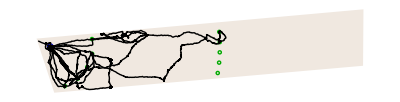
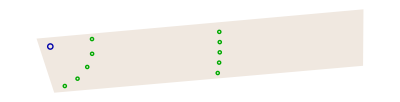
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[metadataGraphic,Graphics[{Thin,Line[DeleteMissing[#[[23]],1,2]]}]]&/@splitRawCoordinates
```

## Distribution of distances

(To determine common distances)

### Individual Sheep

Function to determine the distance between sheep a and b

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]]
```

Running this on two sheep will yield the distance they are from each other at each time step

```mathematica
distances[2,4]
```

{Indeterminate,6.2241,8.98001,13.3817,17.971,22.3762,28.6324,26.5542,210335,142.027,140.091,137.291,137.158,137.012,138.097,138.566,Indeterminate}
 |  |  |  |

Creates a function that for a given sheep and time finds all other sheep within a specified radius

```mathematica
SingleSheepWithinRadius[radius_,sheep_,time_]:=
If[rawCoordinates[[sheep,time]]==={Missing[],Missing[]},
Missing[],Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3],rawCoordinates[[sheep,time]],{All,radius}]]
```

At step 3000, sheep 7 has 3 other sheep with it in less than 50m radius

```mathematica
SingleSheepWithinRadius[50,7,3000]
```

{7,49,12,32}

This allows us to

```mathematica
sheep1herdsize=With[{herd=SingleSheepWithinRadius[100,1,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

24.4138

22

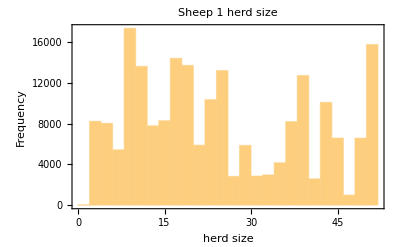

```mathematica
Mean[DeleteMissing[sheep1herdsize]]//N
Median[DeleteMissing[sheep1herdsize]]
Histogram[sheep1herdsize,PlotLabel->"Sheep 1 herd size",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep1herdsize,PlotLabel->"Sheep 1 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

### Mean over all sheep

Set data Directory to export data to

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

Create a function that gets the distances for a pair of sheep and exports the list as an .mx file.

```mathematica
exportDistance[a_,b_]:=
Module[{distance,name},
distance=distances[a,b];
name=StringJoin[ToString[a],"and",ToString[b],".mx"];
Export[FileNameJoin[{dataDirectory,name}],distance]]
```

Generate a list of all the names of the files that were exported.

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
```

Import the data one by one and find the mean and median of each

```mathematica
Module[{currentPairData,data},
data=Table[
currentPairData=DeleteCases[Import[FileNameJoin[{dataDirectory,name}]],Indeterminate];
{Median[currentPairData],Mean[currentPairData]},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
Export[FileNameJoin[{dataDirectory,"medians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"means.mx"}],means];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Missing[]}].

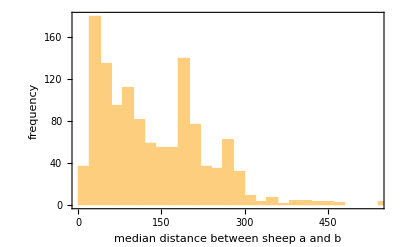

```mathematica
Histogram[medians,Frame->True,FrameLabel->{"median distance between sheep a and b","frequency"}]
```

### Sampling from all pairs

```mathematica
randomDistances=Select[Table[EuclideanDistance@@rawCoordinates2[[RandomInteger[{1,Length[rawCoordinates2]},2],RandomInteger[{1,Length[rawCoordinates2[[1]]]}]]],200000],#>0&]
```

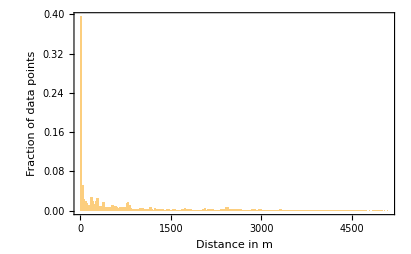

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

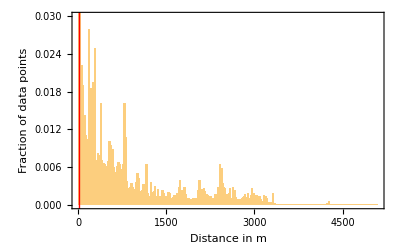

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
Histogram[randomDistances,{50},Frame->True,FrameLabel->{"Distance","count"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

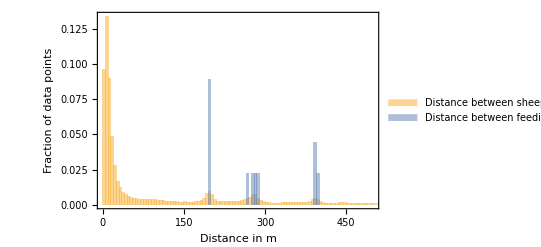

```mathematica
Histogram[{randomDistances,feedingStationsDistances},{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"},ChartLegends->{"Distance between sheep","Distance between feeding stations"}]
```

```mathematica
Histogram[randomDistances,{10},PlotRange->{{0,500},All},Frame->True,FrameLabel-> {"Distances","count"}]
```

### Sampling from all pairs split by interval

```mathematica
splitRandomDistances=Function[coord,Select[Table[EuclideanDistance@@coord[[RandomInteger[{1,Length[coord]},2],RandomInteger[{1,Length[coord[[1]]]}]]],100000],#>0&]]/@splitRawCoordinates2;
```

```mathematica
Dimensions/@splitRandomDistances
```

{{92178},{86218},{93682},{93348}}

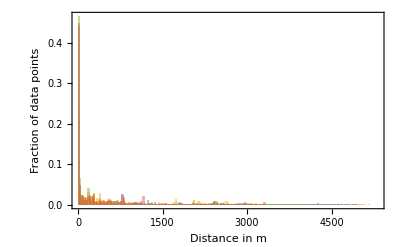

```mathematica
Histogram[splitRandomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

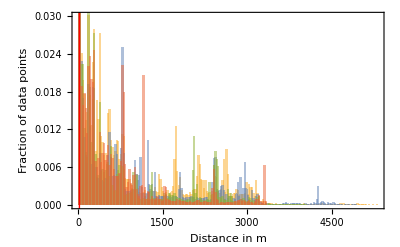

```mathematica
Histogram[splitRandomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;1?1,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Part::span: 2;;1?1 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

DistanceMatrix::mlbddata: The data is not formatted correctly.

Part::span: 2;;1?1 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

DistanceMatrix::mlbddata: The data is not formatted correctly.

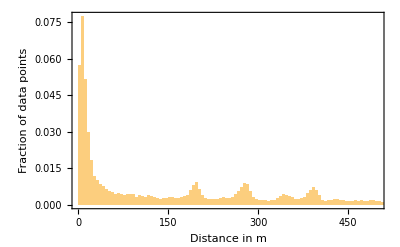
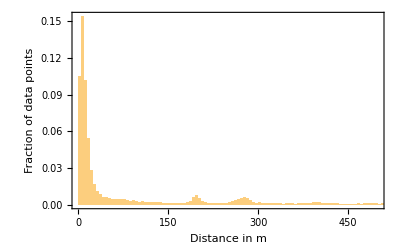
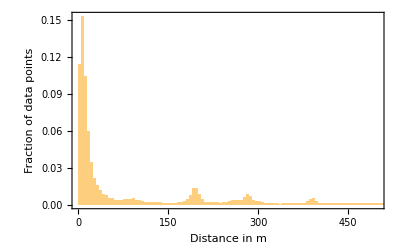
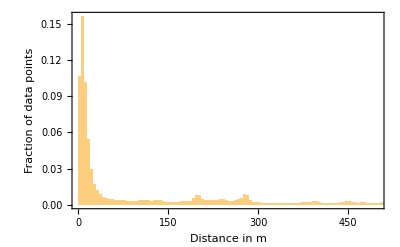

```mathematica
Histogram[splitRandomDistances[[#]],{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"}]&/@Range[4]
```

## Traditional DBSCAN and Clustering

### Simple DBSCAN Implementation

A function that takes a time step and radius and returns a cluster

```mathematica
dbScanClusters[time_,radius_]:=
Module[{positions,rawClusters,outliers},
positions=DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3];
rawClusters=FindClusters[positions,Method->{"DBSCAN","NeighborhoodRadius"->radius,"DropAnomalousValues"->True},DistanceFunction->EuclideanDistance];
outliers=Complement[Values[positions],Flatten[rawClusters]];
Append[rawClusters,outliers]]
```

Plot example radii

```mathematica
dbScanComparison[time_]:=Column[{Show[metadataGraphic,Graphics[Style[Circle[#,50],Thin]&/@DeleteMissing[rawCoordinates[[All,time]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->10},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->30},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],
Show[metadataGraphic,ListPlot[FindClusters[DeleteMissing[rawCoordinates[[All,time]],1,2],Method->{"DBSCAN","NeighborhoodRadius"->50},DistanceFunction->EuclideanDistance],AspectRatio->Automatic],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}]}]
```

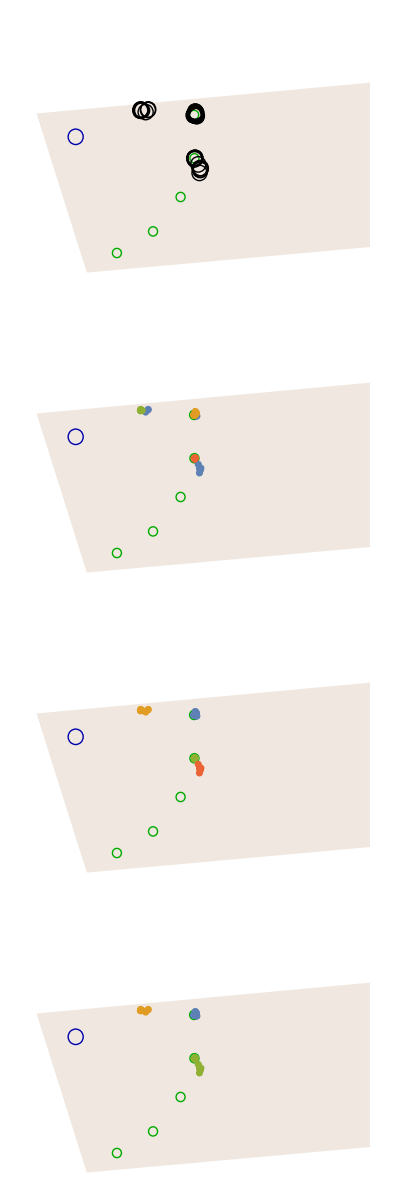

```mathematica
dbScanComparison[1000]
```

### Simple DBSCAN herds production

```mathematica
dbScanHerds5=Table[dbScanClusters[x,5],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx",dbScanHerds5]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx

```mathematica
dbScanHerds10=Table[dbScanClusters[x,10],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx",dbScanHerds10]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds10.mx

```mathematica
dbScanHerds20=Table[dbScanClusters[x,20],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx",dbScanHerds20]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx

```mathematica
dbScanHerds30=Table[dbScanClusters[x,30],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx",dbScanHerds30]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx

```mathematica
dbScanHerds50=Table[dbScanClusters[x,50],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx",dbScanHerds50]
```

```mathematica
dbScanHerds100=Table[dbScanClusters[x,100],{x,1,Length[rawCoordinates[[1]]]}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx",dbScanHerds100]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx

### Simple DBSCAN herds import

```mathematica
dbScanHerds5=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds5.mx"];
dbScanHerds20=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds20.mx"];
dbScanHerds30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx"];
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
dbScanHerds100=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds100.mx"];
```

### Group Stability Simple DBSCAN

```mathematica
dbScanHerds10LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds10;
dbScanHerds30LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds30;
dbScanHerds50LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds50;
```

```mathematica
groupStability10=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds10LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability30=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds30LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,dbScanHerds50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupStability10=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability10.mx"];
```

```mathematica
groupStability30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability30.mx"];
```

### Graph generation Functions

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]];
```

```mathematica
g10=FindFissionFusionGraph[700,800,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g30 =FindFissionFusionGraph[700,800,0.8,dbScanHerds30LonelySheep];
```

```mathematica
g50=FindFissionFusionGraph[700,800,0.8,dbScanHerds50LonelySheep];
```

```mathematica
MinMax[paddock[[All,1]]]
```

{580401,586573}

### Plotting functions

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]*30,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],1]]]]-580401}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Medium],Style["Horizontal distance to western paddock corner (m)",Medium]}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

```mathematica
correctlabels[fig_]:=Show[fig,FrameTicks->ReplacePart[ MapAt[If[#[[2]]==="",#,ReplacePart[#,2->#[[1]]/300]]&,AbsoluteOptions[fig,FrameTicks][[1,2]],{1,All}],{{3},{4}}->None]]
```

### Examples (700-800)

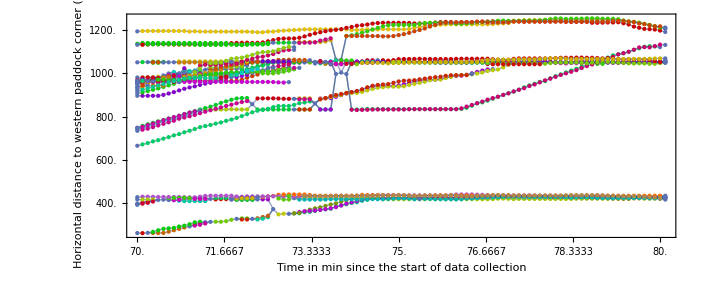

```mathematica
correctlabels[coloredGraph[g10,10000]]
```

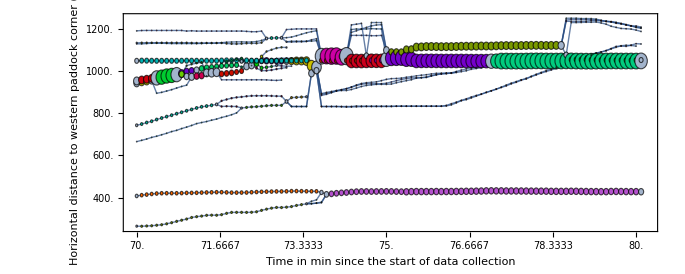

```mathematica
correctlabels[coloredGraph[g30,2000]]
```

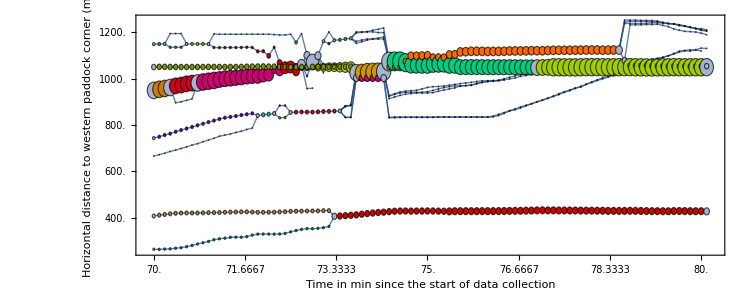

```mathematica
correctlabels[coloredGraph[g50,2000]]
```

#### Influence of Threshold

```mathematica
gstrict=FindFissionFusionGraph[700,800,0.99,dbScanHerds50LonelySheep];
```

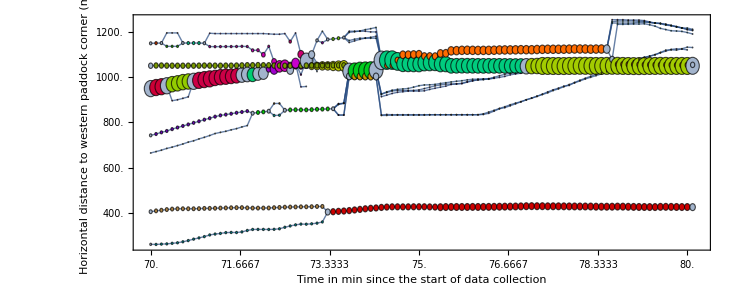

```mathematica
correctlabels[coloredGraph[gstrict,2000]]
```

```mathematica
animation=Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.564282*^6}}],{n,700,800,1}];
```

```mathematica
Export["/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov",animation]
```

/Users/katjad/Documents/Minerva/Capstone/Sheep/ActualMotionAnimation.mov

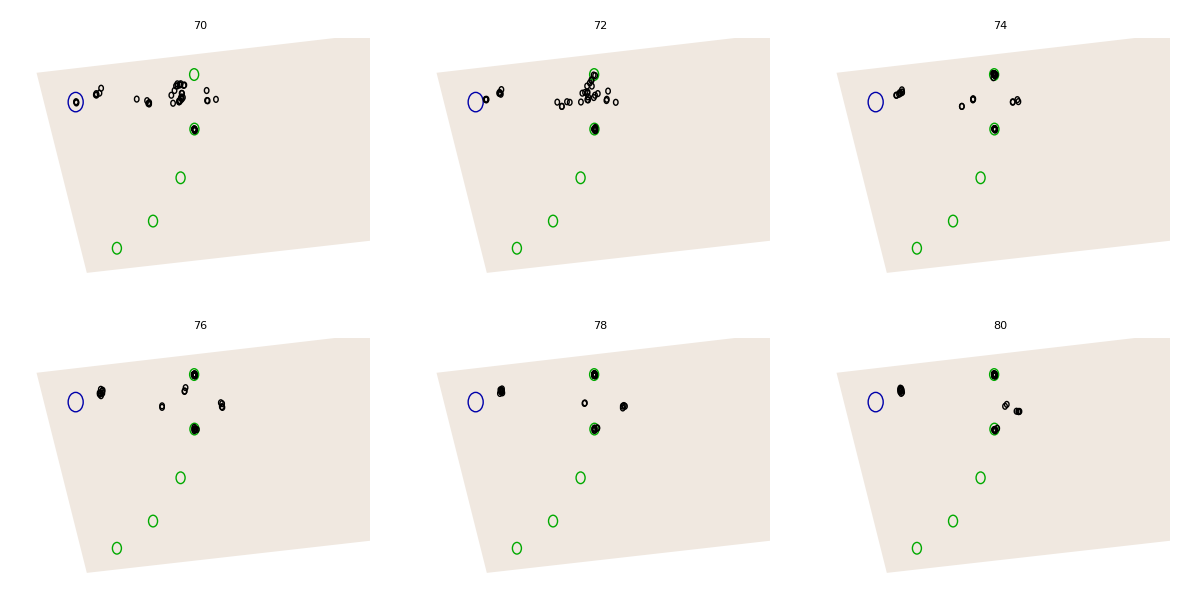

```mathematica
Grid[Partition[Table[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]],PlotRange->{{580401.,582573.},{6.562693*^6,6.563882*^6}},PlotLabel->n/10],{n,700,800,20}],3]]
```

### Group Network Example Two

```mathematica
g10ExampleTwo=FindFissionFusionGraph[150000,150200,0.8,dbScanHerds10LonelySheep];
```

```mathematica
g30ExampleTwo =FindFissionFusionGraph[150000,150200,0.8,dbScanHerds30LonelySheep];
```

```mathematica
g50ExampleTwo=FindFissionFusionGraph[150000,150200,0.8,dbScanHerds50LonelySheep];
```

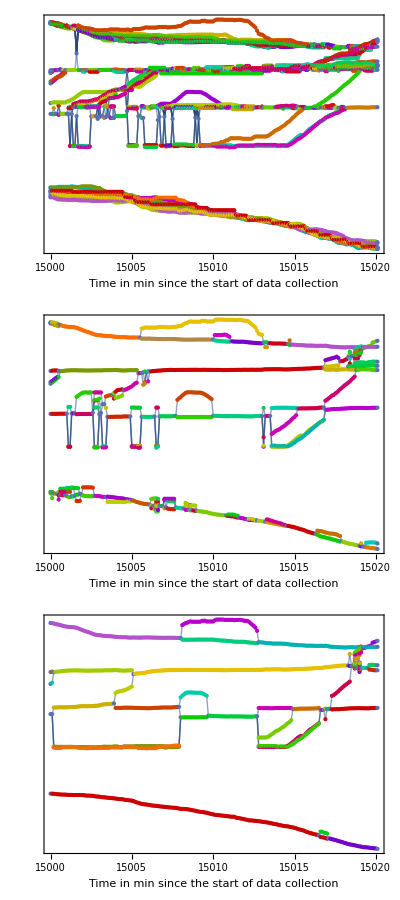

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Column[{coloredGraph[g10ExampleTwo,100],coloredGraph[g30ExampleTwo,100],coloredGraph[g50ExampleTwo,100]}]
```

```mathematica
Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]]],{n,150000,150200,1}]
```

## Sticky DBSCAN

### Definition

```mathematica
determineConnections[pair_,{r1_,r2_}]:=
Module[{split,testList,final},
split=
Catenate/@Split[Split[pair,( #1≤r2&&#2≤r2||#1>r2&&#2>r2||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]r2&&second\[VectorLessEqual]r2||first\[VectorGreater]r2 &&second\[VectorGreater]r2]&];
testList=MemberQ[#,_?(Function[x,x<r1])]&/@split;
final =Catenate[MapIndexed[Table[testList[[First[#2]]],Length[#1]]&,split]]
]
```

```mathematica
symmetricalStickyDBSCAN[data_,{r1_,r2_},{tmin_,tmax_},rawCoordinates_]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,data,{2}]];

MapIndexed[
With[{members=Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{__?NumericQ},{1},Heads->False]]},
ConnectedComponents[Graph[
(*pick vertexes*)
members,
(*pick connections*)
Select[Pick[allEdges,#1,True],FreeQ[Alternatives@@Complement[Range[Length[data]],members]]]]]]&,cons]]
```

### Generate Data

```mathematica
DBSCAN30Sticky50LonelySheep=symmetricalStickyDBSCAN[allPairData,{30,50},{1,210351},rawCoordinates];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN30Sticky50LonelySheep.mx",DBSCAN30Sticky50LonelySheep];
```

```mathematica
DBSCAN30Sticky50LonelySheep=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN30Sticky50LonelySheep.mx"];
```

### Tests

This is just good programming practice for complex pieces of code, so I tested whether different scenarios give the correct result

```mathematica
testData[testdist_]:=MapThread[Transpose[{##}]&,Function[{ps},MapIndexed[#1[[#2[[1]]+1;;]]&,DistanceMatrix[ps]]//N]/@testdist]
```

```mathematica
testcoordsFromDist[testdist_]:=List/@#&/@Transpose[testdist]
```

```mathematica
testDistDBSCAN[testdist_]:=symmetricalStickyDBSCAN[testData[testdist],{30,50},{1,Length[testdist]},testcoordsFromDist[testdist]]//Column
```

#### Expectation: sheep 4 moves from one group to the other group

```mathematica
testdistOneSheepMoves={{1,70,2,60},{2,80,3,6},{2,85,4,8}};
```

```mathematica
testDistDBSCAN[testdistOneSheepMoves]
```

{{1,3},{2,4}}
{{1,3,4},{2}}
{{1,3,4},{2}}

#### Expectation: Apart for the first 3 steps, together for 2, apart for 2

```mathematica
testdistInlargerRadius = {{1,40},{2,40},{2,70},{2,40},{1,20},{1,80},{2,50}};
```

```mathematica
testDistDBSCAN[testdistInlargerRadius]
```

{{1},{2}}
{{1},{2}}
{{1},{2}}
{{1,2}}
{{1,2}}
{{1},{2}}
{{1},{2}}

#### Expectation: One group for 2 steps, two groups for 2 steps

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,100},{1,35,70}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{2,1},{3}}
{{2,1},{3}}

#### Expectation: Together the first 4 steps, then apart for 1

```mathematica
testDistConnected={{1,25,50},{1,35,70},{1,35,Missing[]},{1,35,70},{1,70,Missing[]}};
```

```mathematica
testDistDBSCAN[testDistConnected]
```

{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,2,3}}
{{1,3},{2}}

### Plot

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep];
```

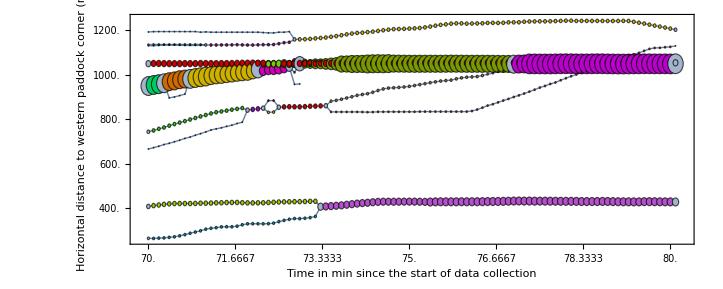

```mathematica
correctlabels[coloredGraph[graph30Sticky50,30]]
```

```mathematica
fullGraph30Sticky50=FindFissionFusionGraph[1,210350,0.8,DBSCAN30Sticky50LonelySheep];
```

$Aborted

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx",fullGraph30Sticky50]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx

```mathematica
EmitSound[SoundNote[]]
```

## Method developed for convenience

Since I will be running the regression repeatedly, I created a function (I also made this publicly available at https://resources.wolframcloud.com/FunctionRepository/resources/RegressionListPlot/ ).
The local definition will be used to make sure everything is reproducible in case I update the public facing version.

### RegressionListPlot

```mathematica
RegressionListPlot[d_,opts:OptionsPattern[]]:=
	Block[{data,x,listplot,listmin,listmax,degree,equations,rsquared},
		data=If[Depth[d]==2,
				{Table[{x,d[[x]]},{x,1,Length[d]}]},
				If[Depth[d]==3,
					{d},
					d]];
		degree=If[Depth[OptionValue["Degree"]]==1,
				Table[OptionValue["Degree"],Length[data]],
				OptionValue["Degree"]];
		equations=Fit[#[[1]],x^(#-1)&/@Range[#[[2]]+1],x]&/@Transpose[{data,degree}];
		rsquared=(Correlation@@Transpose[#])^2&/@data;
		listplot=ListPlot[data,Evaluate[Sequence@@FilterRules[{opts},Options[ListPlot]]]];
		{listmin,listmax}=AbsoluteOptions[listplot,PlotRange][[1,2,1]];
		Show[
			listplot,
			Plot[Evaluate[equations],
			{x,listmin,listmax},
			PlotLegends->If[TrueQ[OptionValue["DisplayEquation"]],
				If[TrueQ[OptionValue["DisplayRSquared"]],
					Row[{equations[[#]],StringTemplate["; \nR^2=``"][rsquared[[#]]]}]&/@Range[Length[equations]],
					equations],
				If[TrueQ[OptionValue["DisplayRSquared"]],
					StringTemplate["R^2=``"][rsquared[[#]]]&/@Range[Length[rsquared]],
					None]],
			Evaluate[Sequence@@FilterRules[{opts},Options[Plot]]]]]]
```

```mathematica
Options[RegressionListPlot]=Join[{"Degree"->1, "DisplayEquation"->False, "DisplayRSquared"->False},Normal@Merge[{Options[Plot],Options[ListPlot]},First]];
```

## Fission-Fusion Analysis

### Locations

#### Absolute locations

```mathematica
fullGraph30Sticky50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx"];
```

```mathematica
mergingEvents =Select[VertexList[fullGraph30Sticky50],VertexInDegree[fullGraph30Sticky50,#]≥2&];
```

```mathematica
splittingEvents =Select[VertexList[fullGraph30Sticky50],VertexOutDegree[fullGraph30Sticky50,#]≥ 2&];
```

```mathematica
mergingCoordinates =Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@mergingEvents;
```

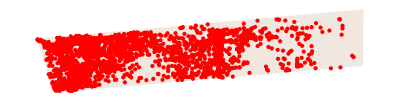

```mathematica
Show[metadataGraphic,Graphics[Style[Point[mergingCoordinates],Red]]]
```

```mathematica
splittingCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@splittingEvents;
```

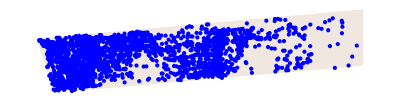

```mathematica
Show[metadataGraphic,Graphics[Style[Point[splittingCoordinates],Blue]]]
```

```mathematica
allCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@VertexList[fullGraph30Sticky50];
```

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
allCoordinatesArray=BinCounts[allCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
Dimensions[allCoordinatesArray]
```

{123,31}

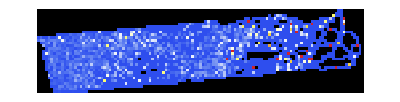

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

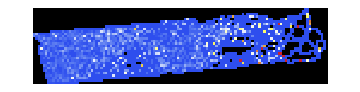

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

#### Regression of distance vs splitting proportion

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
minNumberAllCoordinatesArray=MapAt[If[#<50,Indeterminate,#]&,allCoordinatesArray,{All,All}];
```

```mathematica
splittingProportionArray =Quiet[ splittingArray/minNumberAllCoordinatesArray];
```

```mathematica
minNumberNoDuplicatesArray=MapAt[If[#<25,Indeterminate,#]&,noDuplicatesArray,{All,All}];
```

```mathematica
noDuplicatesSplittingProportionArray =Quiet[ splittingArray/minNumberNoDuplicatesArray];
```

```mathematica
positionArray = Table[{x,y},{x,580401+25,586573-25,50},{y,6.562693*^6+25,6.564282*^6-25,50}];
```

```mathematica
pointsOfInterest=Join[{water},feeding]
```

{{580661,6563573},{581448,6563715},{581450,6563434},{581358,6563183},{581175,6562960},{580935,6562820},{583822,6563068},{583848,6563266},{583860,6563462},{583860,6563657},{583851,6563852}}

```mathematica
distanceArray=MapAt[EuclideanDistance[Catenate[Nearest[pointsOfInterest,#,DistanceFunction->EuclideanDistance]],#]&,positionArray,{All,All}];
```

```mathematica
splittingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[splittingProportionArray]}],{_,Indeterminate}];
```

```mathematica
noDuplicatesSplittingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[noDuplicatesSplittingProportionArray]}],{_,Indeterminate}];
```

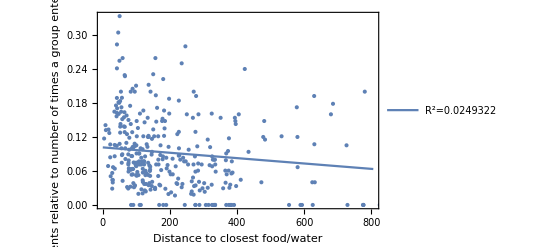

```mathematica
RegressionListPlot[noDuplicatesSplittingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["splitting events relative to \n number of times a group entered the location",Medium]},"DisplayRSquared"->True]
```

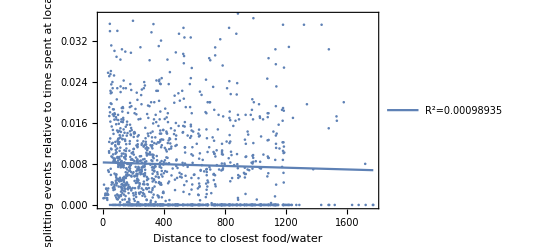

```mathematica
RegressionListPlot[splittingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["splitting events relative to time spent at location",Medium]},"DisplayRSquared"->True]
```

#### Number of times entering the spot

```mathematica
BinCounts[{580401,586573,50},{6.562693*^6,6.564282*^6,50}]
```

```mathematica
allCoordinatesMembersTime ={Mean[rawCoordinates[[#[[1]],#[[2]]]]],#[[1]],#[[2]]}&/@VertexList[fullGraph30Sticky50];
```

```mathematica
groupPaths=Catenate[Function[g,Split[g,(#2[[3]]-#1[[3]])===1&][[All,All,1]]]/@GatherBy[allCoordinatesMembersTime,Sort[#[[2]]]&]];
```

```mathematica
groupPathsNoDuplicates=Function[g,Split[Floor[{#[[1]]-580401,#[[2]]-6.562693*^6}&/@g,50]/50+1][[All,1]]]/@groupPaths;
```

```mathematica
groupPathsNoDuplicates=Function[g,Split[{#[[1]]+580401,#[[2]]+6.562693*^6}&/@Floor[{#[[1]]-580401,#[[2]]-6.562693*^6}&/@g,50]+1][[All,1]]]/@groupPaths;
```

```mathematica
noDuplicatesArray=BinCounts[Catenate[groupPathsNoDuplicates],{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

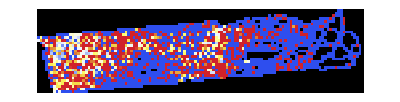

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/noDuplicatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

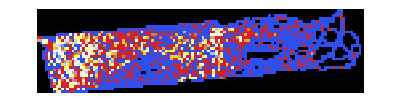

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/noDuplicatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

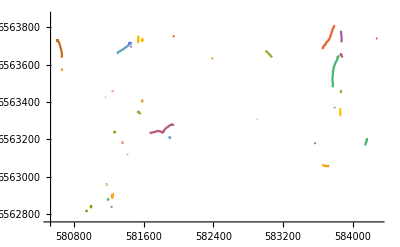

```mathematica
ListLinePlot[RandomSample[groupPaths,50]]
```

```mathematica
groupPathLengths =Total[BlockMap[Apply[EuclideanDistance],#,2,1]]&/@groupPaths;
```

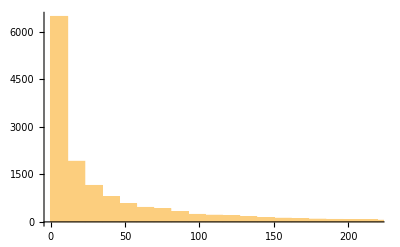

```mathematica
Histogram[groupPathLengths]
```

#### Regression of distance vs merging proportion

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingProportionArray =Quiet[ mergingArray/minNumberAllCoordinatesArray];
```

```mathematica
noDuplicatesMergingProportionArray=Quiet[ mergingArray/minNumberNoDuplicatesArray];
```

```mathematica
mergingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[mergingProportionArray]}],{_,Indeterminate}];
```

```mathematica
noDuplicatesMergingVsDistance=DeleteCases[Thread[{Flatten[distanceArray],Flatten[noDuplicatesMergingProportionArray]}],{_,Indeterminate}];
```

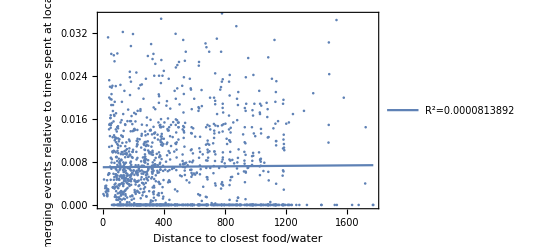

```mathematica
RegressionListPlot[mergingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["merging events relative to time spent at location",Medium]},"DisplayRSquared"->True]
```

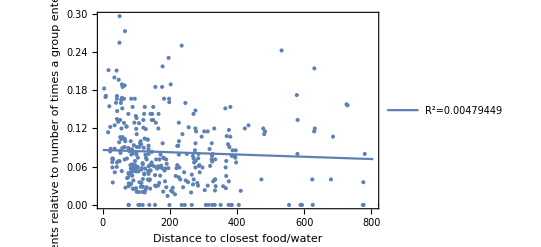

```mathematica
ResourceFunction["RegressionListPlot"][noDuplicatesMergingVsDistance,Frame->True,FrameLabel->{Style["Distance to closest food/water",Medium],Style["merging events relative to \n number of times a group entered the location",Medium]},"DisplayRSquared"->True]
```

### Time

#### Merging

```mathematica
timePoints=rawTs[[2;;]][[mergingEvents[[All,2]],2]];
```

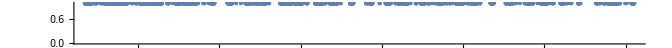

```mathematica
NumberLinePlot[timePoints]
```

```mathematica
dateObjectTimePoints=FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@timePoints;
```

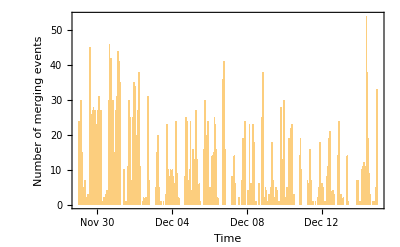

```mathematica
DateHistogram[dateObjectTimePoints,Quantity[1,"Hours"], Frame->True,FrameLabel->{"Time","Number of merging events"}]
```

```mathematica
dateObjectTimePoints[[1]]
```

Thu 29 Nov 2018 15:46:13ACST

```mathematica
hoursTimePoints=DateValue[#,"Hour"]&/@dateObjectTimePoints;
```

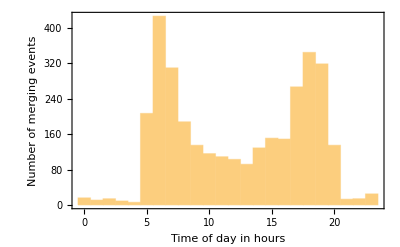

```mathematica
Histogram[hoursTimePoints, Frame->True,FrameLabel->{"Time of day in hours","Number of merging events"}]
```

#### Splitting

```mathematica
splittingTimePoints=rawTs[[2;;]][[splittingEvents[[All,2]],2]];
```

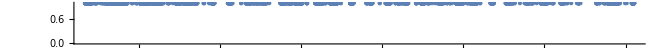

```mathematica
NumberLinePlot[splittingTimePoints]
```

```mathematica
splittingDateObjectTimePoints=FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@splittingTimePoints;
```

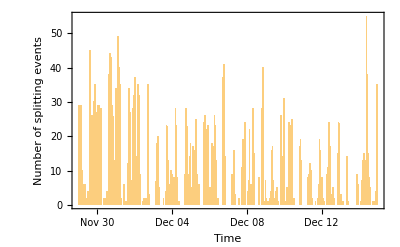

```mathematica
DateHistogram[splittingDateObjectTimePoints,Quantity[1,"Hours"], Frame->True,FrameLabel->{"Time","Number of splitting events"}]
```

```mathematica
splittingHoursTimePoints=DateValue[#,"Hour"]&/@splittingDateObjectTimePoints;
```

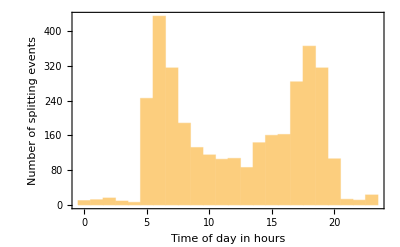

```mathematica
Histogram[splittingHoursTimePoints, Frame->True,FrameLabel->{"Time of day in hours","Number of splitting events"}]
```

#### Combined

```mathematica
DateHistogram[{splittingDateObjectTimePoints,hoursTimePoints},Quantity[1,"Hours"], Frame->True,FrameLabel->{"Time","Number of events"},ChartLegends->{"Splitting Events","Merging Events"}]
```

$Aborted

```mathematica
EmitSound[SoundNote[]]
```

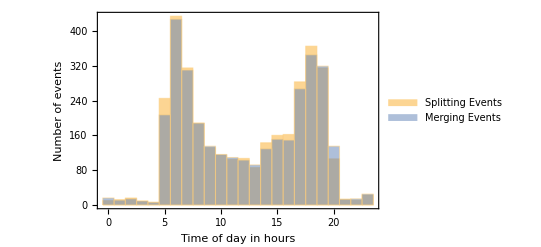

```mathematica
Histogram[{splittingHoursTimePoints,hoursTimePoints}, Frame->True,FrameLabel->{"Time of day in hours","Number of events"},ChartLegends->{"Splitting Events","Merging Events"}]
```

### Density over time

```mathematica
edgeDensityStickyDBSCAN[data_,{r1_,r2_},{tmin_,tmax_},rawCoordinates_]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,data,{2}]];

MapIndexed[
With[{members=Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{__?NumericQ},{1},Heads->False]]},
Length[Select[Pick[allEdges,#1,True],FreeQ[Alternatives@@Complement[Range[Length[data]],members]]]]/Binomial[Length[members],2]//N]&,cons]]
```

```mathematica
allEdgeDensity =edgeDensityStickyDBSCAN[allPairData,{30,50},{1,210351},rawCoordinates];
```

```mathematica
DateListPlot
```

```mathematica
allEdgeDensityTime=Transpose[{FromUnixTime[#,TimeZone->"Australia/Broken_Hill"]&/@rawTs[[2;;,2]],allEdgeDensity}];
```

```mathematica
DateListPlot[allEdgeDensityTime,Frame->True,FrameLabel->{Style["date",Medium],Style["Network Density",Medium]},Joined->False]
```

-Graphics-

```mathematica
byMin=GroupBy[allEdgeDensityTime,DateValue[#[[1]],{"Hour","Minute"}]&];
```

```mathematica
byMinMean=Values[{With[{n=DateValue[#[[1,1]],{"Hour","Minute"}]},n[[1]]+n[[2]]/10//N],Mean[#[[All,2]]]}&/@byMin];
```

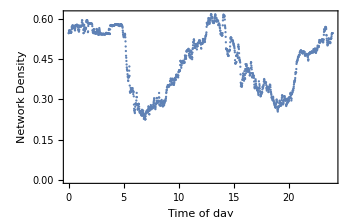

```mathematica
ListPlot[byMinMean, Frame->True,FrameLabel->{Style["Time of day",Medium],Style["Network Density",Medium]}]
```

## Personality data analysis

### Flight Initiation Distance

#### Distribution of FID

```mathematica
rawIDs2=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
```

```mathematica
indexToEartag2=AssociationThread[Range[51],rawIDs2[[2;;,2]]];
```

```mathematica
eartagsToFID=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/eartagsToFID.mx"];
```

```mathematica
indexToFID=indexToEartag2/.eartagsToFID;
```

```mathematica
indexToMeanFID=MapAt[Mean,indexToFID,All]/.Mean["NA"]-> "NA";
```

```mathematica
personalityHerds=DBSCAN30Sticky50LonelySheep/.indexToMeanFID/."NA"-> Missing[];
```

```mathematica
averagePersonality=Mean/@DeleteCases[DeleteCases[Catenate[personalityHerds[[All,1;;-2]]],Missing[],2],{}];
```

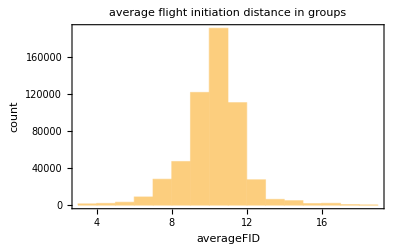

```mathematica
Histogram[averagePersonality,{1},Frame-> True,FrameLabel-> {"averageFID","count"},PlotLabel-> "average flight initiation distance in groups"]
```

```mathematica
splitDBSCAN=BlockMap[DBSCAN30Sticky50LonelySheep[[#[[1]]+1;;#[[2]]]]&,splitSequences,2,1];
```

```mathematica
splitPersonalityHerds=splitDBSCAN/.indexToMeanFID/."NA"-> Missing[];
```

```mathematica
splitAveragePersonality=(Mean/@DeleteCases[DeleteCases[Catenate[#[[All,1;;-2]]],Missing[],2],{}])&/@splitPersonalityHerds;
```

```mathematica
splitAveragePersonality//Length
```

4

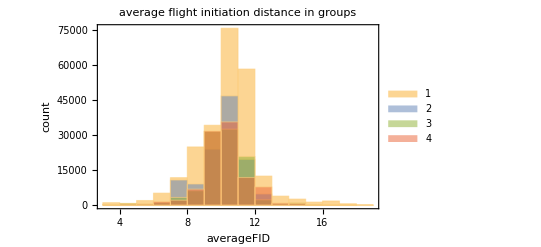

```mathematica
Histogram[splitAveragePersonality,{1},Frame-> True,ChartLegends->Automatic,FrameLabel-> {"averageFID","count"},PlotLabel-> "average flight initiation distance in groups"]
```

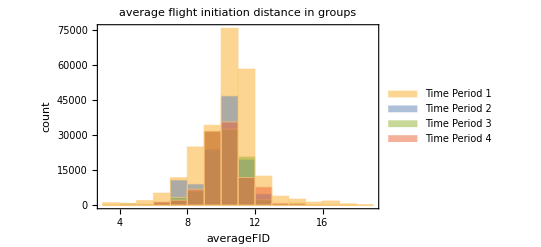

### Exploration Tendency

#### Distribution of Exploration Tendency

```mathematica
explorationRaw=Import["/Users/katjad/Documents/Github/SheepCapstone/buckets.csv","Numeric"->False];
```

```mathematica
flagToET=#[[2]]-> Length[DeleteCases[#[[9;;71-LengthWhile[Reverse[#],Function[x,x==="NA"]]]],"NA"]]/3&/@explorationRaw[[2;;]];
```

Part::take: Cannot take positions 9 through 7 in {29,199,1,1,2018-03-09,NA,Started 10 sec before vid starts,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,«21»}.

```mathematica
eartagToFlags=ToString/@Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/earflags.mx"];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
flagtoMeanET=KeySort[Merge[flagToET,N[Mean[#]]&]];
```

```mathematica
indexToFlag=indexToEartag/.eartagToFlags;
```

```mathematica
indexToMeanET=indexToFlag/.flagtoMeanET;
```

```mathematica
flagToListET=KeySort[Merge[flagToET,#&]];
```

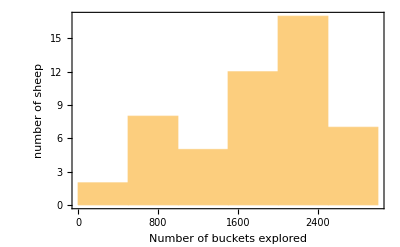

```mathematica
Histogram[Values[indexToMeanET],Frame->True,FrameLabel-> {"Number of buckets explored","number of sheep"}]
```

### Time Alone

#### FID x Time Alone

```mathematica
groupStability30Sticky50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,DBSCAN30Sticky50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability30Sticky50,Length],Length[#]==1&][[ ;;51]];
```

```mathematica
indexToTimeAlone=Association[#->(groupToTimeAlone[{#}]/availableData[[#]])&/@Range[51]];
```

```mathematica
FIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],indexToTimeAlone[x]},{x,51}],{"NA",_}];
```

Because we delete cases for which there is no data, sheep 1711 (index 23) is now index 17.

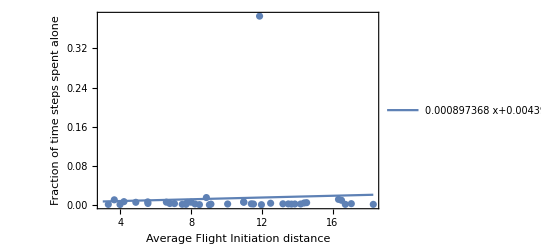

```mathematica
RegressionListPlot[FIDTimeAlone,Frame-> True,FrameLabel-> {Style["Average Flight Initiation distance",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayEquation"->True,"DisplayRSquared"-> True,PlotRange->All]
```

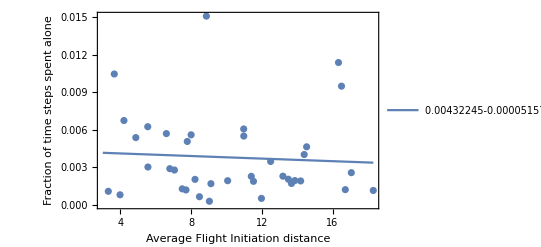

```mathematica
RegressionListPlot[Delete[FIDTimeAlone,17],Frame-> True,FrameLabel-> {Style["Average Flight Initiation distance",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayEquation"->True,"DisplayRSquared"-> True,PlotRange->All]
```

#### FID x Split Time Alone

```mathematica
splitGroupStability30Sticky50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,#,{2}]],First->Last,Join]&/@splitDBSCAN;
```

```mathematica
splitGroupToTimeAlone=(Length/@KeySelect[SortBy[#,Length],Function[x,Length[x]==1]])&/@splitGroupStability30Sticky50;
```

```mathematica
(*splitIndexToTimeAlone=Map[Function[x,Association[#-> If[IntegerQ[x[{#}]],x[{#}],0]&/@Range[51]]],splitGroupToTimeAlone];*)
```

```mathematica
splitIndexToTimeAlone=MapIndexed[Function[{x,i},Association[#-> If[splitAvailableData[[#,i[[1]]]]>1000&&IntegerQ[x[{#}]]&&#=!=17,x[{#}]/splitAvailableData[[#,i[[1]]]],0]&/@Range[51]]],splitGroupToTimeAlone];
```

```mathematica
SplitFIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],#[x]},{x,51}],{"NA",_}]&/@splitIndexToTimeAlone;
```

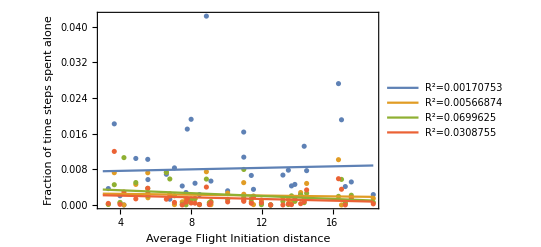

```mathematica
RegressionListPlot[Delete[#,17]&/@SplitFIDTimeAlone,Frame-> True,FrameLabel-> {Style["Average Flight Initiation distance",Medium],Style["Fraction of time steps spent alone",Medium]},"DisplayRSquared"-> True,PlotRange->All]
```

```mathematica
SplitIndexTimeAlone=Catenate[DeleteCases[Table[{x,#[x]},{x,51}],{"NA",_}]&/@splitIndexToTimeAlone];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/indexAndTimeAlone.csv",SplitIndexTimeAlone];
```

#### ET Time Alone

### Average Group Size

#### Data Prep full dataset

```mathematica
indexToGroupLengths30Sticky50=Merge[GeneralUtilities`MonitoredMap[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]],DBSCAN30Sticky50LonelySheep],Identity];
```

```mathematica
indexToMeanGroupLength30Sticky50=Association[#->Mean[indexToGroupLengths30Sticky50[#]]&/@Range[51]];
```

```mathematica
indexToMedianGroupLength30Sticky50=Association[#->Median[indexToGroupLengths30Sticky50[#]]&/@Range[51]];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths30Sticky50.mx",indexToGroupLengths30Sticky50];
```

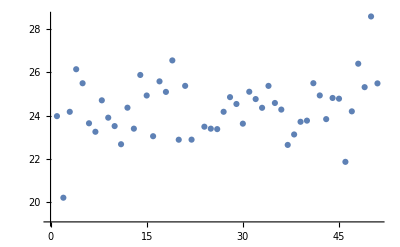

```mathematica
ListPlot[indexToMeanGroupLength30Sticky50]
```

#### Data prep split dataset

```mathematica
splitIndexToGroupLengths30Sticky50=Map[Merge[GeneralUtilities`MonitoredMap[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]],#],Identity]&,splitDBSCAN];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/splitIndexToGroupLengths30Sticky50.mx",splitIndexToGroupLengths30Sticky50];
```

```mathematica
splitIndexToMeanGroupLengths30Sticky50=Function[ti,Association[DeleteCases[Function[in,If[KeyExistsQ[ti,in],in->Mean[ti[in]]]]/@Range[51],Null]]]/@splitIndexToGroupLengths30Sticky50;
```

```mathematica
splitIndexToMeanGroupLengths30Sticky50=Function[ti,Association[DeleteCases[Function[in,If[KeyExistsQ[ti,in],in->Median[ti[in]]]]/@Range[51],Null]]]/@splitIndexToGroupLengths30Sticky50;
```

```mathematica
splitIndexMeanGroupLengthCSV=Catenate[Map[Function[rep,If[KeyExistsQ[rep,#],{#,rep[#]},Nothing]&/@Range[51]],splitIndexToMeanGroupLengths30Sticky50]];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/indexAndTimeAlone.csv",SplitIndexTimeAlone];
```

#### FID x Average Group Size

```mathematica
ResourceFunction["RegressionListPlot"][DeleteCases[Table[{indexToMeanFID[x],indexToMeanGroupLength30Sticky50[x]//N},{x,51}],{"NA",_}],Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True]
```

#### FID x Split Average Group Size

## Code that didn’t make it into the final version for #designthinking

### Dimension Reduction (for y-coordinates on some plots)

To represent the coordinate of each sheep as a single value, I use a dimension-reduction algorithm

```mathematica
trainingData=RandomSample[DeleteMissing[Catenate[rawCoordinates],1,2],100000];
```

```mathematica
linearDR=DimensionReduction[trainingData,1,Method-> "Linear"];
```

```mathematica
linearDimensionReductionData=linearDR[rawCoordinates[[#]]]&/@Range[51];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx",linearDimensionReductionData]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx

```mathematica
linearDimensionReductionData=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/DimensionReduction/linearDimensionReduction.mx"];
```

```mathematica
Dimensions[linearDimensionReductionData]
```

{51,210351,1}

```mathematica
principalComponentDR = DimensionReduction[trainingData,1,Method-> "PrincipalComponentsAnalysis"];
```

```mathematica
latentSemanticAnalysisDR = DimensionReduction[RandomSample[trainingData,100000],1,Method-> "AutoEncoder"];
```

```mathematica
latentSemanticAnalysisDR
```

DimensionReducerFunction[…]

### Sticky DBSCAN (early, non-symmetric version)

```mathematica
(*
Output: clusters for the sheep as traditional DBSCAN but with sheep tending to "stick" to the group they are already with. If r1=r2, equivalent to DBSCAN
Inputs: 
- pts (locations of the sheep, 2D, list of list)
- r1 (smaller of the two radii, sheep are considered together)
-r2(larger of the two radii, sheep are considered together only if they were in the same group in the last time step)
- k (minimum number of neighbors(including oneself) to be considered a core point)
- indexPrevClusters (Association from each cluster to the neighbors in the previous cluster)*)
dbscanSticky[pts_,{r1_,r2_},k_,indexPrevClusters_]:=
Module[{indexPts,nf,pointNeighbors,coreIndices,clusterCores,coreClusters,noncoreIndices,clusterNoncores},
(*Turn points into association with the correct index, delete missing points*)
indexPts=DeleteMissing[AssociationThread[Range[Length[pts]],pts],1,2];
(*Define nearest function*)
nf=Nearest[indexPts];
(*For each point, find its neighbors, considering whether they were neighbors in the previous time step or not*)
pointNeighbors=
Association[MapThread[
#2->With[{prevNeighbors=indexPrevClusters[#2]},
Select[#1,Function[n,
With[{d=EuclideanDistance[indexPts[#2],indexPts[n]]},
If[MemberQ[prevNeighbors,n],d≤r2,d≤r1]
]
]]
]&,
{nf[Values[indexPts],{All,r2}][[All,2;;]],Keys[indexPts]}
]];
(*Find all core points*)
coreIndices=Position[pointNeighbors,_?(Length[#]+1≥k&),{1},Heads->False][[All,1,1]];
(*Form the clusters just from the core points*)
clusterCores=
ConnectedComponents[
Catenate[MapThread[
Thread[#1->#2]&,{
coreIndices,
Select[MemberQ[coreIndices,#]&]/@Lookup[pointNeighbors,coreIndices]
}]]
];
coreClusters=Association[Catenate[MapIndexed[Thread[#1->First[#2]]&,clusterCores]]];
(*Consider all points that are not cores*)
noncoreIndices=Complement[Keys[indexPts],coreIndices];
(*if they could be in more than one cluster, chose randomly*)
clusterNoncores=Merge[Lookup[coreClusters,pointNeighbors[#],Nothing]->#&/@noncoreIndices,Identity];
KeyValueMap[
With[{c=RandomChoice[#1]},clusterCores[[c]]=Join[clusterCores[[c]],#2]]&,
KeyDrop[clusterNoncores,Key[{}]]
];
(*Return the full set of clusters, add an empty list if none of the sheep are alone*)
Append[clusterCores,Lookup[clusterNoncores,Key[{}],{}]]
]
```

```mathematica
fullDBScan[data_,{r1_,r2_},k_,{minTime_,maxTime_}]:=FoldPairList[With[{clustering=dbscanSticky[#2,{r1,r2},k,#1]},{clustering,Join[#1,Association[Catenate[Function[c,#->c&/@c]/@clustering]]]}]&,Association[#->{}&/@Range[Length[data]]],Transpose[data][[minTime;;maxTime]]]
```

```mathematica
DBSCAN30Sticky50 =fullDBScan[rawCoordinates,{30,50},2,{1,210351}];
```

```mathematica
DBSCAN3Sticky5 =fullDBScan[rawCoordinates,{3,5},2,{1,210351}];
```

```mathematica
DBSCAN30Sticky50LonelySheep=Join[Most[#],List/@Last[#]]&/@DBSCAN30Sticky50;
```

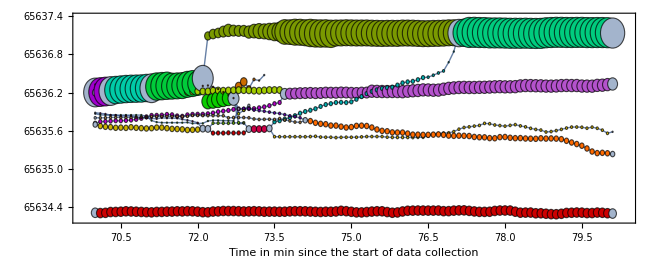

```mathematica
coloredGraph[graph30Sticky50,100]
```

## Cost-benefit of grouping

Cost-benefit function vs foraging alone

```mathematica
costBenefit[size_]:=PDF[NormalDistribution[8,5],size]
```

```mathematica
forageAlone[size_]:=costBenefit[0]
```

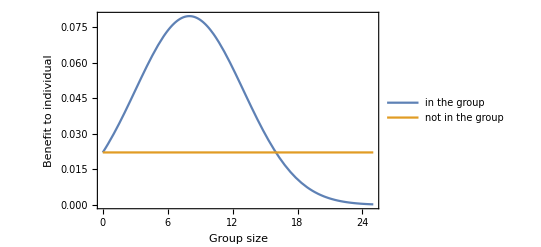

```mathematica
Plot[{costBenefit[x],forageAlone[x]},{x,0,25},Frame->True,FrameLabel->{Style["Group size",Medium],Style["Benefit to individual",Medium]},PlotLegends->Placed[{"in the group","not in the group"},{0.8,0.75}] ]
```